First some definitions

```mathematica
mx=(m0 mstar)/(mstar+σ m0)
my=(m0 mstar)/(mstar-σ m0)
mz = m0
(mx my mz)^(1/3)//Simplify
```

(m0 mstar)/(mstar+m0 σ)

(m0 mstar)/(mstar-m0 σ)

m0

((m0^3 mstar^2)/(mstar^2-m0^2 σ^2))^(1/3)

√(m0 (mstar^2/(-m0^2+mstar^2))^(1/3)) q (√(1/m0+σ/mstar) Cos[θ]+√(1/m0-σ/mstar) Sin[θ])

(√(1/m0-1/mstar) Cos[θ]+√(1/m0+1/mstar) Sin[θ])/(√(1/m0+1/mstar) Cos[θ]+√(1/m0-1/mstar) Sin[θ])

(√(1/m0-1/mstar))/(√(1/m0+1/mstar))

(√(1/m0+1/mstar))/(√(1/m0-1/mstar))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

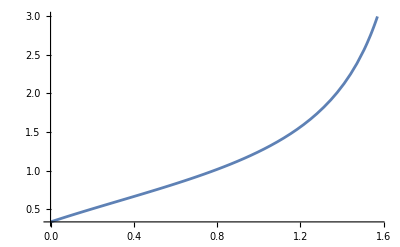

{(-mdown+mup q)/(√(-4 mdown mup q+mdown^2 (1+q^2)+mup^2 (1+q^2))),(mdown-mup q)/(√(-4 mdown mup q+mdown^2 (1+q^2)+mup^2 (1+q^2)))}

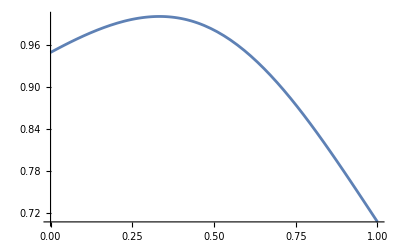

```mathematica
mDOS=m0(mstar^2/(mstar^2-m0^2))^(1/3);
qprime=q √mDOS(Cos[θ] √((mstar+ σ m0)/(m0 mstar))+Sin[θ] √((mstar-σ m0)/(m0 mstar)))//Simplify
qratio=Assuming[m0>0&&mstar>0&&mstar>m0,Simplify[(qprime/.σ->-1)/(qprime/.σ->1)]]
qratio/.θ->0
qratio/.θ->π/2
Solve[(qratio/.θ->0)==x,mstar];
Plot[(mup Cos[θ]+mdown Sin[θ])/(mdown Cos[θ]+mup Sin[θ])/.{mup->1,mdown->3},{θ,0,π/2}]
Assuming[mup>mdown,SolveValues[(mup Cos[θ]+mdown Sin[θ])/(mdown Cos[θ]+mup Sin[θ])==q,θ]//Cos//Simplify//Normal]
Plot[Max[%//.{mup->1,mdown->3}],{q,0,1}]
```

```mathematica
qprime/.σ->1
```

√((m0 mstar^2)/(-m0^2+mstar^2)) q (√(1/m0+1/mstar) Cos[θ]+√(1/m0-1/mstar) Sin[θ])

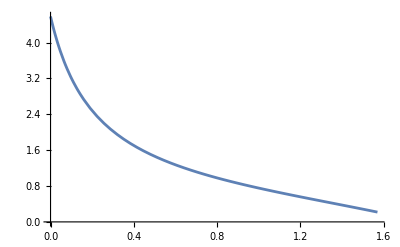

```mathematica
Plot[qratio^-1/.{m0->1,mstar->1.1},{θ,0,π/2}]
```

Now first define the full function F

```mathematica
F=((1+Δ)(1-z/2 Log[(z+1)/(z-1)])/.z->qs vs )+(1-Δ)(+1/2-(1-(numin)^2)/(4q)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)])/.{nuplus->vs+1/2 q,numin->vs-1/2 q}//Simplify;
Ffull=((1+Δ)(+1/2-(1-(numin)^2)/(4q qsup)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q qsup)Log[(nuplus+1)/(nuplus-1)])/.{nuplus->qsup^-1 vs+1/2 qsup q,numin->qsup^-1 vs-1/2 qsup q})+(1-Δ)(+1/2-(1-(numin)^2)/(4q qsdown)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q qsdown)Log[(nuplus+1)/(nuplus-1)])/.{nuplus->qsdown^-1 vs+1/2 qsdown q,numin->qsdown^-1 vs-1/2 qsdown q}//Simplify;
Fcomplete=((1+Δ)(1-z/2 Log[(z+1)/(z-1)])/.z->qsup vs )+(1-Δ)(+1/2-(1-(numin)^2)/(4q)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)])/.{nuplus->qsdown^-1 vs+1/2 qsdown q,numin->qsdown^-1 vs-1/2 qsdown q}//Simplify;
```

1+1/2 (2-vs Log[(1+vs)/(-1+vs)])-1/2 qs vs Log[(1+qs vs)/(-1+qs vs)]

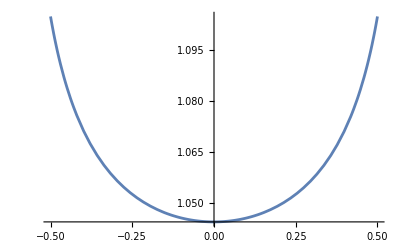

```mathematica
F0q=SeriesCoefficient[F,{q,0,0}]/.Δ->0
Plot[{vs/.{FindRoot[Re[F0q]==0,{vs,1.1}]}},{qs,-0.5,0.5}]
```

```mathematica
Series[F/.Δ->0,{q,0,-1},{qs,0,1}]//Normal
Solve[%==0,vs]
Plot[vs/.%,{q}]
```

Piecewise[{{(qs^2 vs)/2+1/16 qs (-4 ⅈ π+4 (-1+vs^2) Log[(1+vs)/(-1+vs)]), Im[-2 qs vs-2 qs^2 vs^2-2 qs^3 vs^3]<0}, {(qs^2 vs)/2+1/16 qs (4 ⅈ π+4 (-1+vs^2) Log[(1+vs)/(-1+vs)]), True}}]/q

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[Piecewise[{{(qs^2 vs)/2+1/16 qs (-4 ⅈ π+4 (-1+vs^2) Log[(1+vs)/(-1+vs)]), Im[-2 qs vs-2 qs^2 vs^2-2 qs^3 vs^3]<0}, {(qs^2 vs)/2+1/16 qs (4 ⅈ π+4 (-1+vs^2) Log[(1+vs)/(-1+vs)]), True}}]/q==0,vs]

Plot::pllim: Range specification {q} is not of the form {x, xmin, xmax}.

Plot[vs/.%,{q}]

Let us first look at the solutions for no magnetic field

(qs^2 vs)/2+1/4 qs (-1+vs^2) Log[(1+vs)/(-1+vs)]

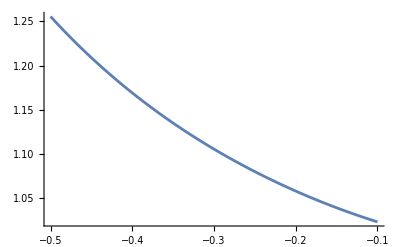

```mathematica
F0q=(qs^2 vs)/2+1/16 qs (4 (-1+vs^2) Log[(1+vs)/(-1+vs)])
Plot[{vs/.{FindRoot[Re[F0q]==0,{vs,1.001}]}},{qs,-0.1,-0.5}]
```

```mathematica
Solve[F0q==0,vs]
Series[F0q,{vs,1,1}]
Solve[Normal[%]==0,vs]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[(qs^2 vs)/2+1/4 qs (-1+vs^2) Log[(1+vs)/(-1+vs)]==0,vs]

qs^2/2+1/2 (qs^2+qs Log[2/(-1+vs)]) (vs-1)+O[vs-1]^2

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[qs^2/2+1/2 (-1+vs) (qs^2+qs Log[2/(-1+vs)])==0,vs]

```mathematica
(*vs0=Solve[Assuming[{qs,vs}∈Reals,Normal[Series[F0q,{vs,2,1}]]]==0,vs]*)
Plot[{vs/.{FindRoot[Re[F0q]==0,{vs,1.001}]},Re[vs/.vs0[[1]]]},{qs,0.1,0.5}]
Plot[{vs/.{FindRoot[Re[F0q]==0,{vs,1.001}]},Re[vs/.vs0[[1]]]},{qs,-0.1,-0.5}]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {9.99918 ((0.200687+3.14159 ⅈ) (-1+0.0100016 Plus[«2»])-2 (-1+vs) (0.100008+Log[Times[«2»]]))==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {9.99918 ((0.200687+3.14159 ⅈ) (-1.+0.0100016 Plus[«2»])-2. (-1.+vs) (0.100008+Log[Times[«2»]]))==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {9.24458 ((0.217193+3.14159 ⅈ) (-1+0.0117011 Plus[«2»])-2 (-1+vs) (0.108171+Log[Times[«2»]]))==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {-2.00003 ((-1.09859+3.14159 ⅈ) (-1+0.249992 Plus[«2»])-2 (-1+vs) (-0.499992+Log[Times[«2»]]))==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-2.00003 ((-1.09859+3.14159 ⅈ) (-1.+0.249992 Plus[«2»])-2. (-1.+vs) (-0.499992+Log[Times[«2»]]))==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {-2.03323 ((-1.07694+3.14159 ⅈ) (-1+0.241895 Plus[«2»])-2 (-1+vs) (-0.491829+Log[Times[«2»]]))==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted

Showing that we cannot find an actual analytical solution that is accurate, but we can find it at small q

```mathematica
Series[F0q/.qs->0,{vs,1,0}]//Simplify
Solve[(%//Normal)==0,vs]
%//N
vs0=NSolve[(F0q/.qs->0)==0,vs]//Simplify//Normal
%//N
```

1/2 (4-Log[2/(-1+vs)])+O[vs-1]^1

{{vs→(2+ⅇ^4)/ⅇ^4}}

{{vs→1.03663}}

{{vs→1.04438}}

{{vs→1.04438}}

Now look at the g-factor

```mathematica
Ffull=SeriesCoefficient[F,{q,0,0}]//Simplify
```

1/2 (4+vs (-1+Δ) Log[(1+vs)/(-1+vs)]-qs vs (1+Δ) Log[(1+qs vs)/(-1+qs vs)])

1/2 (4-Log[2/(-1+vs)]+Δ Log[2/(-1+vs)])

{{vs→ConditionalExpression[1+2 ⅇ^(4/(-1+Δ)), -π<-4 Im[1/(-1+Δ)]≤π]}}

{ConditionalExpression[(1+2/ⅇ^4)-(8 Δ)/ⅇ^4+O[Δ]^2, -π<-4 Im[1/(-1+Δ)]≤π]}

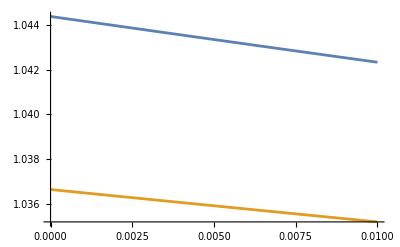

```mathematica
Series[Ffull/.qs->0,{vs,1,0}]//Normal
solDelta=Solve[%==0,vs]//Simplify
Series[vs/.solDelta,{Δ,0,1}]
Plot[{vs/.FindRoot[(Ffull/.qs->0)==0,{vs,1.1}],vs/.solDelta[[1]]},{Δ,0,0.01}]
```

And now look at the quality factor

(vs (1/(-1+vs^2)+δ^2/(-1+vs^2 δ^2))-1/2 Log[(1+vs)/(-1+vs)]-1/2 δ Log[(1+vs δ)/(-1+vs δ)])/q+O[q]^0

(4 (vs (1/(-1+vs^2)+δ^2/(-1+vs^2 δ^2))-1/2 Log[(1+vs)/(-1+vs)]-1/2 δ Log[(1+vs δ)/(-1+vs δ)]))/(π δ)+O[q]^1

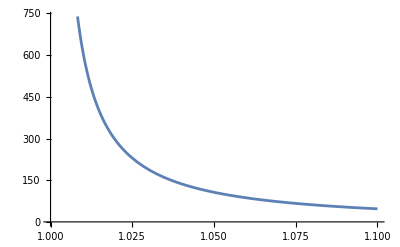

(Piecewise[{{(4 (vs/(-1+vs^2)-1/2 Log[(1+vs)/(-1+vs)]))/(π δ)-2 ⅈ+O[δ]^1, Im[vs δ]≤0}, {(4 (vs/(-1+vs^2)-1/2 Log[(1+vs)/(-1+vs)]))/(π δ)+2 ⅈ+O[δ]^1, True}}])+O[q]^1

```mathematica
dF=D[(1+1/2-(1-(numin)^2)/(4q)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)]),nuplus]/q+D[(1+1/2-(1-(numin)^2)/(4q)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)]),numin]/q//Simplify;
dFvs=Series[(dF/.{nuplus->vs+1/2 q,numin->vs-1/2 q})+dF/.{nuplus->vs δ+1/2 q δ,numin->vs δ-1/2 q δ},{q,0,-1}]//Simplify
Q=(q 4dFvs)/(π δ)//Simplify
Plot[Re[Normal[Q]/.δ->0.1],{vs,1,1.1}]
Series[Q,{δ,0,0}]//Simplify
```

Solving the eigenvalue problem

```mathematica
chidownapprox=Series[(+1/2-(1-(numin)^2)/(4q)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)])/.{numin->w/(q vF)-q/2,nuplus->w/(q vF)+q/2},{w,0,1}]
Limit[%,q->0]
```

(1/2+((-4+q^2) (Log[-2+q]-Log[2+q]))/(16 q)-((-4+q^2) Log[(2+q)/(-2+q)])/(16 q))+((-Log[-2+q]+Log[2+q]-Log[(2+q)/(-2+q)]) w)/(4 q vF)+O[w]^2

Indeterminate